```mathematica
AdvantageMean[n_,m_]:=(1/n^m)Sum[(-1)^(m+s+1)Binomial[m,s]HarmonicNumber[n,-s-1],{s,0,m-1}];
AdvantageMeanApproxLimitN[n_,m_]:=(n*m)/(m+1)+1/2;
```

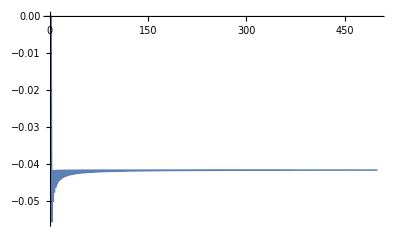

```mathematica
DiscretePlot[N[AdvantageMean[n,Ceiling[n/2]]-AdvantageMeanApproxLimitN[n,Ceiling[n/2]]],{n,1,500},PlotRange->All,PlotStyle->Thin,Filling->None,Joined->True]
```

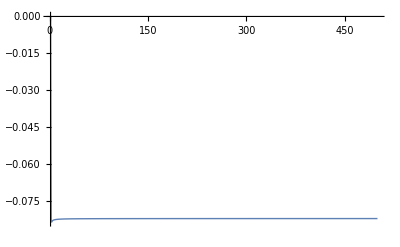

```mathematica
DiscretePlot[N[AdvantageMean[n,n]-AdvantageMeanApproxLimitN[n,n]],{n,1,500},PlotRange->All,PlotStyle->Thin,Filling->None,Joined->True]
```

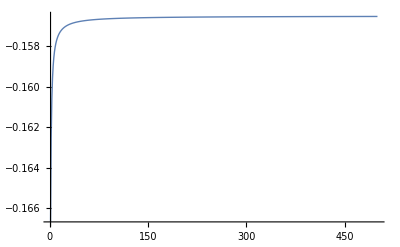

```mathematica
DiscretePlot[N[AdvantageMean[n,2n]-AdvantageMeanApproxLimitN[n,2n]],{n,1,500},PlotRange->All,PlotStyle->Thin,Filling->None,Joined->True]
```

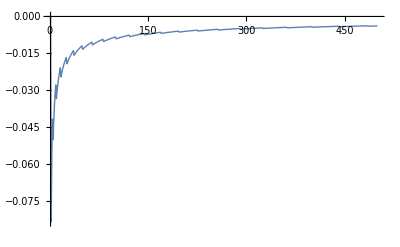

```mathematica
DiscretePlot[N[AdvantageMean[n,Ceiling[Sqrt[n]]]-AdvantageMeanApproxLimitN[n,Ceiling[Sqrt[n]]]],{n,1,500},PlotRange->All,PlotStyle->Thin,Filling->None,Joined->True]
```

```mathematica
Simplify[Normal[Series[(1/n^m)(-1)^(m+s+1)Binomial[m,s]HarmonicNumber[n,-s-1],{m,Infinity,0}]],{n≥0,m≥0}]
```

((-1)^(1+m+s) m^s n^-m HarmonicNumber[n,-1-s])/(s Gamma[s])

```mathematica
AdvantageMeanApproxLimitM[n_,m_]:=Sum[((-1)^(1+m+s) m^s n^-m HarmonicNumber[n,-1-s])/(s Gamma[s]),{s,0,m-1}];
```

```mathematica
Simplify[Normal[Series[AdvantageMeanApproxLimitM[n,m],{m,Infinity,1}]],{n≥0,m≥0}]
```

∑_(s=0)^(-1+m) ((-1)^(1+m+s) m^s n^-m HarmonicNumber[n,-1-s])/(s Gamma[s])

```mathematica
Simplify[Normal[Series[With[{m=a*n},(1/n^m)(-1)^(m+s+1)Binomial[m,s]HarmonicNumber[n,-s-1]],{n,Infinity,0}]],{a≥0,s≥0,n≥0,m≥0,s<a*n,s∈Integers,n∈Integers,m∈Integers}]
```

-((-1/n)^(a n) (-a n)^s (n^(1+s) (2+2 n+s)+2 (2+s) Zeta[-1-s]))/(2 s (2+s) Gamma[s])